Routines for YODA plotting

from: https://yoda.hepforge.org/trac/wiki/DataFormat

```mathematica
<<(NotebookDirectory[]<>"../../atom_mathematica.m")
```

```mathematica
Zmm=(GetYodaRaw[NotebookDirectory[]<>"Zmm.yoda"]);
```

1 Imported ..Histo1D..  /ATLAS_1603_09222/Mee/0

2 Imported ..Histo1D..  /ATLAS_1603_09222/Mmm/0

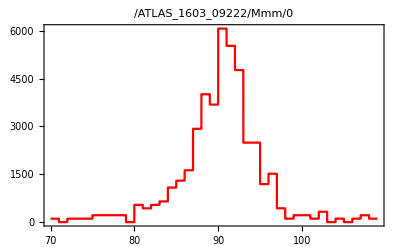

```mathematica
Hmm=HistogramPlot[Zmm[[2]],PlotStyle->{Red}]
```

```mathematica
Zee=(GetYodaRaw[NotebookDirectory[]<>"Zee.yoda"]);
```

1 Imported ..Histo1D..  /ATLAS_1603_09222/Mee/0

2 Imported ..Histo1D..  /ATLAS_1603_09222/Mmm/0

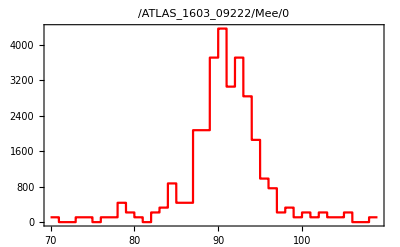

```mathematica
Hee=HistogramPlot[Zee[[1]],PlotStyle->{Red}]
```

```mathematica
ATLASZee=(GetYodaRaw[NotebookDirectory[]<>"ATLAS_Zee.yoda"]);
```

1 Imported ..Scatter2D..  /REF/d01-x01-y01

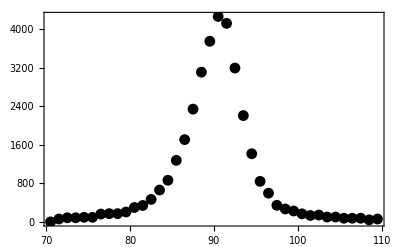

```mathematica
AZee=ScatterPlot[ATLASZee[[1]],PlotStyle->{Black}]
```

1 Imported ..Scatter2D..  /REF/d01-x01-y01

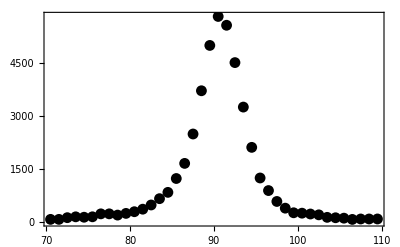

```mathematica
ATLASZmm=(GetYodaRaw[NotebookDirectory[]<>"ATLAS_Zmm.yoda"]);
AZmm=ScatterPlot[ATLASZmm[[1]],PlotStyle->{Black}]
```

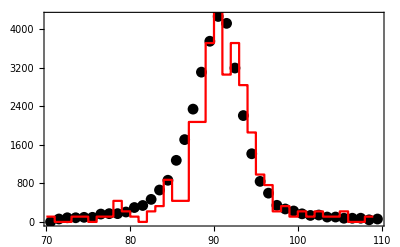

```mathematica
Show[AZee,Hee]
```

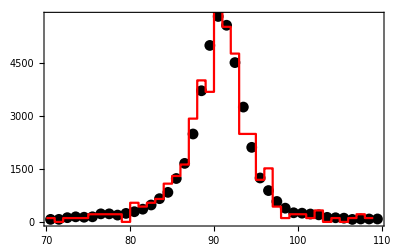

```mathematica
Show[AZmm,Hmm]
```